# Staggered chemical potential and the surface bands of Sr_2 RuO_4

Anirudh Chandrasekaran

Loughborough University
14 June 2024

In this notebook we will examine the effect of a staggered chemical potential on the dispersion of the surface bands of Sr_2 RuO_4. We will focus in particular on the M point. The staggered chemical potential breaks the lattice reflection symmetry but preserves the fourfold rotation symmetry about each Ru atom. As we will see below, this allows the two d_xy bands at the M point to decouple and become individually four-fold symmetric. This allows the bands to host X_9 singularities under tuning.

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Sr2RuO4"]<>"Package"];
<<BandUtilities`
```

## Interpolating between the Wannier90 files

### Ingredients needed for symmetrization

```mathematica
ρ={{0,-1,0},{1,0,0},{0,0,1}}; (*The matrix part of the Subscript[C, 4] rotation about one of the Ru atoms.*)
Uρ={{0,-1,0},{1,0,0},{0,0,-1}}; (*Representation of Subscript[C, 4] rotation in the d-orbital space.*)

rxy={{0,1,0},{1,0,0},{0,0,1}};  (*x<->y reflection.*)
Urxy={{-1,0,0},{0,1,0},{0,0,-1}}; (*Representation of the x<->y reflection.*)

c0={1/4,3/4,0}; (*Location of one of the Ru atoms, which we shall use as the centre of the Subscript[C, 4] rotation.*)

AtomLocations={{3/4,1/4,0},{3/4,1/4,0},{3/4,1/4,0},{1/4,3/4,0},{1/4,3/4,0},{1/4,3/4,0}}; (*Location of the basis atoms in the fractional coordinates within the unit cell.*)

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]]}];

AppendTo[SymmetryList,{MatrixPower[ρ,i].rxy,(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]].ArrayFlatten[{{0,1},{1,0}}⊗Urxy]}];
,{i,1,4}];
```

### Interpolation with symmetrization

We now interpolate between the Wannier90 data for 13 different rotations of the RuO octahedra: 0° through 12° to generate a continuously θ dependent Hamiltonian, whilst ensuring that the interpolated model has the right symmetry (for which we are feeding the list SymmetryList):

```mathematica
FileLocn=NotebookDirectory[]<>"unrenormalized2/";

W90Data=LoadInterpolateTBMs[{FileLocn<>"Sr2RuO4_0deg.dat",FileLocn<>"Sr2RuO4_1deg.dat",FileLocn<>"Sr2RuO4_2deg.dat",FileLocn<>"Sr2RuO4_3deg.dat",FileLocn<>"Sr2RuO4_4deg.dat",FileLocn<>"Sr2RuO4_5deg.dat",FileLocn<>"Sr2RuO4_6deg.dat",FileLocn<>"Sr2RuO4_7deg.dat",FileLocn<>"Sr2RuO4_8deg.dat",FileLocn<>"Sr2RuO4_9deg.dat",FileLocn<>"Sr2RuO4_10deg.dat",FileLocn<>"Sr2RuO4_11deg.dat",FileLocn<>"Sr2RuO4_12deg.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"Symmetries"->SymmetryList,"OrbitalCentres"->AtomLocations,"ParameterSymbol"->"θ"];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 6

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {741,853,853,853,845,853,853,853,853,853,853,853,853}

Interpolating between the Hamiltonians.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 79

Since this is largely an exploratory analysis, we will not include the overall band renormalization or the spin orbit term which have minimal impact on the M point. We begin by adding a staggered chemical potential Δ

```mathematica
Hamltn1[k1_,k2_,θ_,Δ_]=W90Data[[1]]+DiagonalMatrix[{Δ,Δ,Δ,-Δ,-Δ,-Δ}];
```

## Tuning to a HOS with non - zero Δ

We begin by defining a version of the Hamiltonian suitable for series expansion (once again in the bulk Brillouin zone basis for the sake of consistency)

```mathematica
Ham[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],k[[4]]]
```

To compute the Hessian determinant with δθ and δΔ corrections, we need to series expand the dispersion to quadratic order with corrections. To find the bands closest to Fermi level to series expand, we first calculate the eigenvalues at the M point for a small Δ=0.005 (that is 5 meV).

```mathematica
Sort[Eigenvalues[Ham[{0,π//N,8,0.005}]]]
```

{-0.555813,-0.555813,-0.076319,-0.066319,0.286847,0.286847}

It is clear that bands 3 and 4 are the bands of interest closest to the Fermi level. We will plot these bands with orbital projection once the critical θ has been figured out.

### Band 3

```mathematica
TaylA=Chop[TaylorExpandBand[Ham,{0,π//N,8,0.005},3,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylA]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.076319-1. δΔ+(-0.0205955+0.00119685 δθ) δθ+(-0.014985+8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_x^2+(-0.014985-8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_y^2

We note that the quadratic term contains a very small δΔ correction. This indicates that the critical θ does not depend strongly on Δ (as long as it is non-zero and small. For large Δ, this analysis based on series expansion to quadratic order may not hold).

We can compute the Hessian determinant and solve for δθ by setting it to zero:

```mathematica
HesDet=((D[TaylA[[3]],{p1,2}]D[TaylA[[3]],{p2,2}])-(D[TaylA[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln1=Solve[HesDet==0,δθ]
```

0.000898201-0.00384658 δθ+0.00414751 δθ^2-0.000062584 δθ^3+2.37766×10^-7 δθ^4

{{δθ→0.468682},{δθ→0.468682},{δθ→131.14},{δθ→131.14}}

The critical θ to the first approximation is then given by

```mathematica
TaylB=Chop[TaylorExpandBand[Ham,{0,π//N,8+δθ/.Soln1[[1]],0.005},3,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylB]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0856538-1. δΔ+(-0.0191726+0.00162093 δθ) δθ+(0.0000166482-3.94981×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_x^2+(0.0000166482+3.94981×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_y^2

Indeed the coefficients of the quadratic terms have become quite small. We can repeat the process once again to obtain better convergence

```mathematica
HesDet=((D[TaylB[[3]],{p1,2}]D[TaylB[[3]],{p2,2}])-(D[TaylB[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln2=Solve[HesDet==0,δθ]
```

1.10864×10^-9+4.25488×10^-6 δθ+0.00408246 δθ^2-0.0000351289 δθ^3+7.55692×10^-8 δθ^4

{{δθ→-0.000521115},{δθ→-0.000521115},{δθ→232.429},{δθ→232.429}}

Thus, the critical theta is given by

```mathematica
θcrit=8+(δθ/.Soln1[[1]])+(δθ/.Soln2[[1]])
```

8.46816

Using this, we go ahead and define the Hamiltonian at the critical θ:

```mathematica
HamCrit[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θcrit,0.005]
```

```mathematica
TaylC=Chop[TaylorExpandBand[HamCrit,{0,π//N},3,4,"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylC]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0856438-0.630949 k_x^4+0.102619 k_x^3 k_y+0.860439 k_x^2 k_y^2-0.102619 k_x k_y^3-0.630949 k_y^4

This is obviously a singularity belonging to the X_9 class. We can confirm this explicitly

```mathematica
DiagnoseHOS[Total[TaylC]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]
```

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

{2,8,5}

We can also explicitly check that this satisfies the four fold rotation symmetry (k_x,k_y)->(k_y,-k_x) but not the mirror symmetry (k_x,k_y)->(k_y,k_x) since the latter is broken while the former is preserved under the staggered chemical potential Δ.

```mathematica
Chop[((TaylC/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC/.{p1->Subscript[k, y],p2->-Subscript[k, x]}))//FullSimplify,10^-6]//Total
Chop[((TaylC/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC/.{p1->Subscript[k, y],p2->Subscript[k, x]}))//FullSimplify,10^-6]//Total
```

0

0.205239 k_x^3 k_y-0.205239 k_x k_y^3

The 3D and surface plot of the dispersion

```mathematica
Plot3D[Total[TaylC],{p1,-1/4,1/4},{p2,-1/4,1/4}]
```

-Graphics3D-

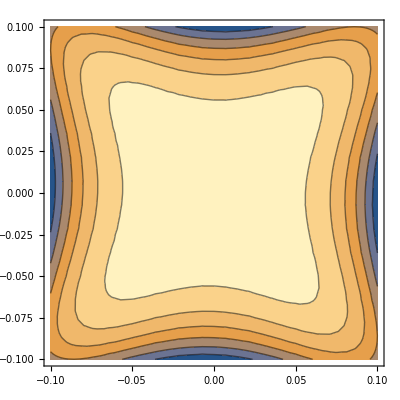

```mathematica
ContourPlot[Total[TaylC],{p1,-1/10,1/10},{p2,-1/10,1/10}]
```

These indicate that this is a four fold maximum rather than a saddle.

### Band 4

```mathematica
TaylA2=Chop[TaylorExpandBand[Ham,{0,π//N,8,0.005},4,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylA2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.066319+1. δΔ+(-0.0205955+0.00119685 δθ) δθ+(-0.014985-8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_x^2+(-0.014985+8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_y^2

We note that the quadratic term contains a very small δΔ correction. This indicates that the critical θ does not depend strongly on Δ (as long as it is non-zero and small. For large Δ, this analysis based on series expansion to quadratic order may not hold).

We can compute the Hessian determinant and solve for δθ by setting it to zero:

```mathematica
HesDet=((D[TaylA2[[3]],{p1,2}]D[TaylA2[[3]],{p2,2}])-(D[TaylA2[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln12=Solve[HesDet==0,δθ]
```

0.000898201-0.00384658 δθ+0.00414751 δθ^2-0.000062584 δθ^3+2.37766×10^-7 δθ^4

{{δθ→0.468682},{δθ→0.468682},{δθ→131.14},{δθ→131.14}}

The critical θ to the first approximation is then given by

```mathematica
TaylB2=Chop[TaylorExpandBand[Ham,{0,π//N,8+δθ/.Soln12[[1]],0.005},4,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylB2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0756538+1. δΔ+(-0.0191726+0.00162093 δθ) δθ+(0.0000166482-9.02946×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_x^2+(0.0000166482+9.02946×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_y^2

Indeed the coefficients of the quadratic terms have become quite small. We can repeat the process once again to obtain better convergence

```mathematica
HesDet=((D[TaylB2[[3]],{p1,2}]D[TaylB2[[3]],{p2,2}])-(D[TaylB2[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln22=Solve[HesDet==0,δθ]
```

1.10864×10^-9+4.25488×10^-6 δθ+0.00408246 δθ^2-0.0000351289 δθ^3+7.55692×10^-8 δθ^4

{{δθ→-0.000521115},{δθ→-0.000521115},{δθ→232.429},{δθ→232.429}}

Thus, the critical theta is given by

```mathematica
θcrit2=8+(δθ/.Soln12[[1]])+(δθ/.Soln22[[1]])
```

8.46816

Using this, we go ahead and define the Hamiltonian at the critical θ:

```mathematica
HamCrit2[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θcrit2,0.005]
```

```mathematica
TaylC2=Chop[TaylorExpandBand[HamCrit2,{0,π//N},4,4,"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylC2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0756438+0.201354 k_x^4-0.102619 k_x^3 k_y-0.804168 k_x^2 k_y^2+0.102619 k_x k_y^3+0.201354 k_y^4

This is obviously a singularity belonging to the X_9 class. We can confirm this explicitly

```mathematica
DiagnoseHOS[Total[TaylC2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]
```

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

{2,8,5}

We can also explicitly check that this satisfies the four fold rotation symmetry (k_x,k_y)->(k_y,-k_x) but not the mirror symmetry (k_x,k_y)->(k_y,k_x) since the latter is broken while the former is preserved under the staggered chemical potential Δ.

```mathematica
Chop[((TaylC2/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC2/.{p1->Subscript[k, y],p2->-Subscript[k, x]}))//FullSimplify,10^-6]//Total
Chop[((TaylC2/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC2/.{p1->Subscript[k, y],p2->Subscript[k, x]}))//FullSimplify,10^-6]//Total
```

0

-0.205239 k_x^3 k_y+0.205239 k_x k_y^3

The 3D and surface plot of the dispersion

```mathematica
Plot3D[Total[TaylC2],{p1,-1/4,1/4},{p2,-1/4,1/4}]
```

-Graphics3D-

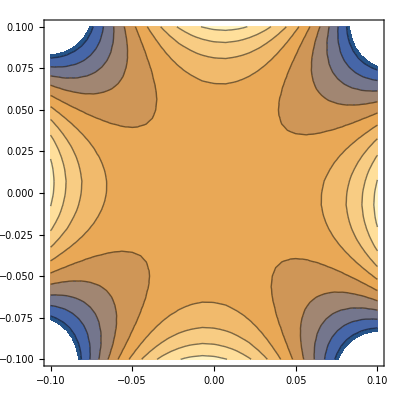

```mathematica
ContourPlot[Total[TaylC2],{p1,-1/10,1/10},{p2,-1/10,1/10}]
```

These confirm that this is a genuine four fold saddle.

### Comparing bands 3 and 4

We can finally compare the HOS in band 3 and band 4 (recall that these bands were degenerate before the staggered chemical potential was applied)

```mathematica
Total[TaylC]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
Total[TaylC2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0856438-0.630949 k_x^4+0.102619 k_x^3 k_y+0.860439 k_x^2 k_y^2-0.102619 k_x k_y^3-0.630949 k_y^4

-0.0756438+0.201354 k_x^4-0.102619 k_x^3 k_y-0.804168 k_x^2 k_y^2+0.102619 k_x k_y^3+0.201354 k_y^4

It is clear that while band 3 (with negative k_x^4 and k_y^4 terms) and band 4 (with positive k_x^4 and k_y^4 terms) disperse roughly in the opposite fashion. This is obviously an approximate qualification since the k_x^2 k_y^2 terms also play a role. We now plot the band structure with orbital projections

```mathematica
δk=3.869  0.35;
HSymmPts={{{-δk,π-δk},"← -M_x"},{{0,π},"M_y"},{{0,π+δk+0.01},"Γ →"}};
Bnds=GenerateBandStructure[HamCrit,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,4},{2,5},{3,6}}];
```

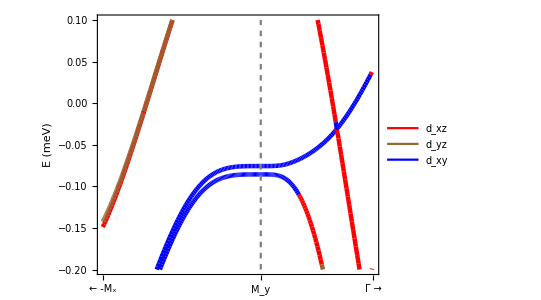

```mathematica
PlotBandStructure[Bnds,(*{-0.042,0.012}*){-0.2,0.1},AspectRatio->3/4,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)13,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{13,Black,"Arial"},"yTicks"->{12,Black,"Helvetica"},"LineThickness"->0.008,"LineColorScheme"->{Red,Brown,Blue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},(*,Legend*)"PlotKeyLegend"->{{"d_xz","d_yz","d_xy"},{0.25,0.85}}]
```

We notice that the M point singularities arise primarily from the d_xy orbitals. Further the higher order saddle nature of band 4 and the higher order maximum nature of band 3 are quite apparent.